```mathematica
home="/Users/rjones/repo/EXT/Notes/Notebooks";
SetDirectory[home];
Directory[]
NotebookEvaluate[home<>"/GaussianOverlapBase.nb"];
```

/Users/rjones/repo/EXT/Notes/Notebooks

cart to sph map: {√(x^2+y^2+z^2),ArcTan[z,√(x^2+y^2)],ArcTan[x,y]}

sph polar map:{r Cos[phi] Sin[theta],r Sin[phi] Sin[theta],r Cos[theta]}

A= (-1/(√2) | 0 | 1/(√2)
-ⅈ/(√2) | 0 | -ⅈ/(√2)
0 | 1 | 0)

```mathematica
A ={{-1/Sqrt[2],0,I/Sqrt[2]},
{0,1,0},
{-1/Sqrt[2],0,-I/Sqrt[2]}};
A ={{-I/Sqrt[2],0,1/Sqrt[2]},
{0,1,0},
{-I/Sqrt[2],0,-1/Sqrt[2]}};
At = ConjugateTranspose[A];
D1toR[D1mat_List] := A.D1mat.At;
RtoD1[Rmat_List] := At.Rmat.A;


Print[MatrixForm[A]];
Det[A]
```

(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

ⅈ

```mathematica
DD = D1[a1,a2,a3];
Print["D=",MatrixForm[DD]];
d1 ={Exp[-I a1],1,Exp[I a1]}
dd = {{(1+Cos[a3])/2,-Sin[a3]/Sqrt[2],(1-Cos[a3])/2},
{Sin[a3]/Sqrt[2],Cos[a3],-Sin[a3]/Sqrt[2]},
{(1-Cos[a3])/2,Sin[a3]/Sqrt[2],(1+Cos[a3])/2}};
d2 ={Exp[-I a2],1,Exp[I a2]}
Print["d=",MatrixForm[dd]];
(* MatrixForm[FullSimplify[Inverse[DD].dd]] *)
Dd = Table[d1[[i]] dd[[i,j]] d2[[j]],{i,3},{j,3}];
Print["exp dd exp = ",MatrixForm[Dd]]
```

D=(ⅇ^(-ⅈ a1-ⅈ a2) Cos[a3/2]^2 | -√2 ⅇ^(-ⅈ a1) Cos[a3/2] Sin[a3/2] | ⅇ^(-ⅈ a1+ⅈ a2) Sin[a3/2]^2
√2 ⅇ^(-ⅈ a2) Cos[a3/2] Sin[a3/2] | Cos[a3] | -√2 ⅇ^(ⅈ a2) Cos[a3/2] Sin[a3/2]
ⅇ^(ⅈ a1-ⅈ a2) Sin[a3/2]^2 | √2 ⅇ^(ⅈ a1) Cos[a3/2] Sin[a3/2] | ⅇ^(ⅈ a1+ⅈ a2) Cos[a3/2]^2)

{ⅇ^(-ⅈ a1),1,ⅇ^(ⅈ a1)}

{ⅇ^(-ⅈ a2),1,ⅇ^(ⅈ a2)}

d=(1/2 (1+Cos[a3]) | -Sin[a3]/(√2) | 1/2 (1-Cos[a3])
Sin[a3]/(√2) | Cos[a3] | -Sin[a3]/(√2)
1/2 (1-Cos[a3]) | Sin[a3]/(√2) | 1/2 (1+Cos[a3]))

exp dd exp = (1/2 ⅇ^(-ⅈ a1-ⅈ a2) (1+Cos[a3]) | -(ⅇ^(-ⅈ a1) Sin[a3])/(√2) | 1/2 ⅇ^(-ⅈ a1+ⅈ a2) (1-Cos[a3])
(ⅇ^(-ⅈ a2) Sin[a3])/(√2) | Cos[a3] | -(ⅇ^(ⅈ a2) Sin[a3])/(√2)
1/2 ⅇ^(ⅈ a1-ⅈ a2) (1-Cos[a3]) | (ⅇ^(ⅈ a1) Sin[a3])/(√2) | 1/2 ⅇ^(ⅈ a1+ⅈ a2) (1+Cos[a3]))

```mathematica
DD = D1[a1,a2,0];
Print[MatrixForm[At],MatrixForm[DD],MatrixForm[A]]
Print[MatrixForm[At.DD],MatrixForm[A]]
R=FullSimplify[At.DD.A];
MatrixForm[R]
```

(ⅈ/(√2) | 0 | ⅈ/(√2)
0 | 1 | 0
1/(√2) | 0 | -1/(√2))(ⅇ^(-ⅈ a1-ⅈ a2) | 0 | 0
0 | 1 | 0
0 | 0 | ⅇ^(ⅈ a1+ⅈ a2))(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

((ⅈ ⅇ^(-ⅈ a1-ⅈ a2))/(√2) | 0 | (ⅈ ⅇ^(ⅈ a1+ⅈ a2))/(√2)
0 | 1 | 0
ⅇ^(-ⅈ a1-ⅈ a2)/(√2) | 0 | -ⅇ^(ⅈ a1+ⅈ a2)/(√2))(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

(Cos[a1+a2] | 0 | Sin[a1+a2]
0 | 1 | 0
-Sin[a1+a2] | 0 | Cos[a1+a2])

```mathematica
DD = D1[0,0,a3];
Print[MatrixForm[At],MatrixForm[DD],MatrixForm[A]]
Print[MatrixForm[At.DD],MatrixForm[A]]
R=FullSimplify[At.DD.A];
MatrixForm[R]
```

(ⅈ/(√2) | 0 | ⅈ/(√2)
0 | 1 | 0
1/(√2) | 0 | -1/(√2))(Cos[a3/2]^2 | -√2 Cos[a3/2] Sin[a3/2] | Sin[a3/2]^2
√2 Cos[a3/2] Sin[a3/2] | Cos[a3] | -√2 Cos[a3/2] Sin[a3/2]
Sin[a3/2]^2 | √2 Cos[a3/2] Sin[a3/2] | Cos[a3/2]^2)(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

((ⅈ Cos[a3/2]^2)/(√2)+(ⅈ Sin[a3/2]^2)/(√2) | 0 | (ⅈ Cos[a3/2]^2)/(√2)+(ⅈ Sin[a3/2]^2)/(√2)
√2 Cos[a3/2] Sin[a3/2] | Cos[a3] | -√2 Cos[a3/2] Sin[a3/2]
Cos[a3/2]^2/(√2)-Sin[a3/2]^2/(√2) | -2 Cos[a3/2] Sin[a3/2] | -Cos[a3/2]^2/(√2)+Sin[a3/2]^2/(√2))(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

(1 | 0 | 0
0 | Cos[a3] | Sin[a3]
0 | -Sin[a3] | Cos[a3])

```mathematica
DD = D1[a1,a2,a3];
Print[MatrixForm[At],MatrixForm[DD],MatrixForm[A]]
Print[MatrixForm[At.DD],MatrixForm[A]]
R=FullSimplify[At.DD.A];
MatrixForm[R]

MatrixForm[FullSimplify[RtoD1[R]-DD]]
```

(ⅈ/(√2) | 0 | ⅈ/(√2)
0 | 1 | 0
1/(√2) | 0 | -1/(√2))(ⅇ^(-ⅈ a1-ⅈ a2) Cos[a3/2]^2 | -√2 ⅇ^(-ⅈ a1) Cos[a3/2] Sin[a3/2] | ⅇ^(-ⅈ a1+ⅈ a2) Sin[a3/2]^2
√2 ⅇ^(-ⅈ a2) Cos[a3/2] Sin[a3/2] | Cos[a3] | -√2 ⅇ^(ⅈ a2) Cos[a3/2] Sin[a3/2]
ⅇ^(ⅈ a1-ⅈ a2) Sin[a3/2]^2 | √2 ⅇ^(ⅈ a1) Cos[a3/2] Sin[a3/2] | ⅇ^(ⅈ a1+ⅈ a2) Cos[a3/2]^2)(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

((ⅈ ⅇ^(-ⅈ a1-ⅈ a2) Cos[a3/2]^2)/(√2)+(ⅈ ⅇ^(ⅈ a1-ⅈ a2) Sin[a3/2]^2)/(√2) | -ⅈ ⅇ^(-ⅈ a1) Cos[a3/2] Sin[a3/2]+ⅈ ⅇ^(ⅈ a1) Cos[a3/2] Sin[a3/2] | (ⅈ ⅇ^(ⅈ a1+ⅈ a2) Cos[a3/2]^2)/(√2)+(ⅈ ⅇ^(-ⅈ a1+ⅈ a2) Sin[a3/2]^2)/(√2)
√2 ⅇ^(-ⅈ a2) Cos[a3/2] Sin[a3/2] | Cos[a3] | -√2 ⅇ^(ⅈ a2) Cos[a3/2] Sin[a3/2]
(ⅇ^(-ⅈ a1-ⅈ a2) Cos[a3/2]^2)/(√2)-(ⅇ^(ⅈ a1-ⅈ a2) Sin[a3/2]^2)/(√2) | -ⅇ^(-ⅈ a1) Cos[a3/2] Sin[a3/2]-ⅇ^(ⅈ a1) Cos[a3/2] Sin[a3/2] | -(ⅇ^(ⅈ a1+ⅈ a2) Cos[a3/2]^2)/(√2)+(ⅇ^(-ⅈ a1+ⅈ a2) Sin[a3/2]^2)/(√2))(-ⅈ/(√2) | 0 | 1/(√2)
0 | 1 | 0
-ⅈ/(√2) | 0 | -1/(√2))

(Cos[a1] Cos[a2]-Cos[a3] Sin[a1] Sin[a2] | -Sin[a1] Sin[a3] | Cos[a2] Cos[a3] Sin[a1]+Cos[a1] Sin[a2]
-Sin[a2] Sin[a3] | Cos[a3] | Cos[a2] Sin[a3]
-Cos[a2] Sin[a1]-Cos[a1] Cos[a3] Sin[a2] | -Cos[a1] Sin[a3] | Cos[a1] Cos[a2] Cos[a3]-Sin[a1] Sin[a2])

((1/2+ⅈ/2) (Cos[a2] (ⅈ+Cos[a3]) Sin[a1]+Cos[a1] (1+ⅈ Cos[a3]) Sin[a2]) | -(-1)^(3/4) (Cos[a1]+(1-ⅈ) Sin[a1]) Sin[a3] | (1/2-ⅈ/2) (Cos[a1] (Cos[a2] (-1+Cos[a3])+(1-ⅈ) Sin[a2])+Sin[a1] ((1-ⅈ) Cos[a2] Cos[a3]+(-1+Cos[a3]) Sin[a2]))
(-1)^(1/4) (-Cos[a2]+(1+ⅈ) Sin[a2]) Sin[a3] | 0 | (-1)^(3/4) Sin[a2] Sin[a3]
(1/2+ⅈ/2) (-Sin[a1] ((1+ⅈ) Cos[a2]+Sin[a2]-Cos[a3] Sin[a2])+Cos[a1] (Cos[a2] (-1+Cos[a3])-(1+ⅈ) Cos[a3] Sin[a2])) | -(-1)^(1/4) Sin[a1] Sin[a3] | (-1/2-ⅈ/2) (Cos[a2] (ⅈ+Cos[a3]) Sin[a1]+Cos[a1] (1+ⅈ Cos[a3]) Sin[a2]))

```mathematica
lmax =1;
Print[MatrixForm[Ys =Table[
SphericalHarmonicY[lmax,m,theta,phi],
{m,-lmax,lmax}]]];
MatrixForm[RIYs =Table[FullSimplify[{Re[Ys[[i]]],Im[Ys[[i]]]},Assumptions->{Im[theta]==0,Im[phi]==0}],{i,3}]]
GraphicsGrid[Table[{
SphericalPlot3D[Abs[Re[SphericalHarmonicY[lmax,m,theta,phi]]],theta,phi],
SphericalPlot3D[Abs[Im[SphericalHarmonicY[lmax,m,theta,phi]]],theta,phi]}, {m,-lmax,lmax}]]
```

(1/2 ⅇ^(-ⅈ phi) √(3/(2 π)) Sin[theta]
1/2 √(3/π) Cos[theta]
-1/2 ⅇ^(ⅈ phi) √(3/(2 π)) Sin[theta])

(1/2 √(3/(2 π)) Cos[phi] Sin[theta] | -1/2 √(3/(2 π)) Sin[phi] Sin[theta]
1/2 √(3/π) Cos[theta] | 0
-1/2 √(3/(2 π)) Cos[phi] Sin[theta] | -1/2 √(3/(2 π)) Sin[phi] Sin[theta])

-Graphics-

```mathematica
(* if all points have the same radial distance W is singular *)
T={{1,1,1},
1.1*{1,-1,-1},
1.2*{-1,1,-1},
1.3*{-1,-1,1}};
R=Rangle[Pi/4,0,0];
Print["R=",MatrixForm[R]]
Print["D=",MatrixForm[RtoD1[R]]]
RT =Rot[R,T];
lmax = 1;
sval = 1;
XA = RT;
XB = 1.01T;
Clear[W,YA,YB,J];
Print["X_A=",MatrixForm[XA],"   X_B=",MatrixForm[XB]];
W = Wmatrix[XA,XB,lmax,sval];
Print["W=",MatrixForm[N[W]]]
YA = Ymatrix[XA,lmax,sval];
YB = Ymatrix[XB,lmax,sval];
Print["Y_A=",MatrixForm[N[YA]],"\nY_B=",MatrixForm[N[YB]]];
J = YA.W.ConjugateTranspose[YB];
Print["Yt W Y =",MatrixForm[N[J]]];
Print["Yt Y =",MatrixForm[N[YA.ConjugateTranspose[YB]]]];
```

R=(1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1)

D=(1/2+1/(2 √2) | -ⅈ/2 | -ⅈ/2+ⅈ/(2 √2)
-ⅈ/2 | 1/(√2) | 1/2
ⅈ/2-ⅈ/(2 √2) | -1/2 | 1/2+1/(2 √2))

X_A=(0 | √2 | 1
1.55563 | 0. | -1.1
-1.69706 | 0. | -1.2
0. | -1.83848 | 1.3)   X_B=(1.01 | 1.01 | 1.01
1.111 | -1.111 | -1.111
-1.212 | 1.212 | -1.212
-1.313 | -1.313 | 1.313)

W=(1.74233 | 1.70732 | 1.64003 | 1.54617
1.71273 | 1.69309 | 1.64164 | 1.56308
1.65095 | 1.64734 | 1.61324 | 1.55222
1.56234 | 1.57443 | 1.55808 | 1.51574)

Y_A=(0.-0.282095 ⅈ | 0.282095 | -0.282095-3.45466×10^-17 ⅈ | 1.72733×10^-17+0.282095 ⅈ
0.282095 | -0.282095 | -0.282095 | 0.282095
0.-0.282095 ⅈ | -0.282095 | 0.282095-3.45466×10^-17 ⅈ | -1.72733×10^-17+0.282095 ⅈ)
Y_B=(0.199471-0.199471 ⅈ | 0.199471+0.199471 ⅈ | -0.199471-0.199471 ⅈ | -0.199471+0.199471 ⅈ
0.282095 | -0.282095 | -0.282095 | 0.282095
-0.199471-0.199471 ⅈ | -0.199471+0.199471 ⅈ | 0.199471-0.199471 ⅈ | 0.199471+0.199471 ⅈ)

Yt W Y =(0.00939132-0.0093925 ⅈ | -0.000119572+0.00035194 ⅈ | 0.00170623+0.013172 ⅈ
-0.000424507-0.000209012 ⅈ | 0.000242154+0. ⅈ | 0.000424507-0.000209012 ⅈ
0.00170623-0.013172 ⅈ | 0.000119572+0.00035194 ⅈ | 0.00939132+0.0093925 ⅈ)

Yt Y =(0.225079-0.225079 ⅈ | 4.87271×10^-18+1.38778×10^-17 ⅈ | 6.93889×10^-18-6.93889×10^-18 ⅈ
6.93889×10^-18-1.38778×10^-17 ⅈ | 0.31831+0. ⅈ | -6.93889×10^-18-1.38778×10^-17 ⅈ
6.93889×10^-18+6.93889×10^-18 ⅈ | -4.87271×10^-18+1.38778×10^-17 ⅈ | 0.225079+0.225079 ⅈ)

```mathematica
Chop[N[Tr[J]]]
I1mat =Imatrix[XA,XB,lmax,sval];
mform[I1mat]
Chop[N[Tr[I1mat]]]
Chop[N[dotS[XA,XB,lmax,sval]]]
```

0.0190248

(0.00939132+0.0093925 ⅈ | -0.000424507+0.000209012 ⅈ | 0.00170623+0.013172 ⅈ
-0.000119572-0.00035194 ⅈ | 0.000242154 | 0.000119572-0.00035194 ⅈ
0.00170623-0.013172 ⅈ | 0.000424507+0.000209012 ⅈ | 0.00939132-0.0093925 ⅈ)

0.0190248

0.0190248

```mathematica
Clear[U1,S,U2];
{U1,S,U2} = SingularValueDecomposition[J];
Print["tr Yt W Y =",N[Tr[J]]];
Print["S = ",MatrixForm[Chop[N[S]]]]
Print["U1 = ",MatrixForm[Chop[N[U1]]]]
Print["U2 = ",MatrixForm[Chop[N[U2]]]]
U = ConjugateTranspose[U1].U2;
Print["R= ",MatrixForm[Chop[N[D1toR[U]]]]]
Print["U = ",MatrixForm[Chop[N[U]]]]
Print["U is unitary: ",Norm[Chop[N[U.ConjugateTranspose[U]]-IdentityMatrix[3]]]==0]
```

tr Yt W Y =0.0190248+0. ⅈ

S = (0.0265779 | 0 | 0
0 | 0.000228794 | 0
0 | 0 | 1.56314×10^-7)

U1 = (-0.706879 | -0.017969 | 0.707106
0.00817425+0.024001 ⅈ | -0.385049-0.922546 ⅈ | -0.00161324+0.000549514 ⅈ
-0.559936+0.431452 ⅈ | -0.0126373+0.0127743 ⅈ | -0.560078+0.431638 ⅈ)

U2 = (-0.499869-0.499931 ⅈ | -0.0100451-0.0099996 ⅈ | 0.499977+0.500022 ⅈ
0.00644877+0.0189347 ⅈ | -0.385096-0.922659 ⅈ | -0.00122848+0.000418454 ⅈ
-0.0908187+0.701108 ⅈ | 0.0000442419+0.0141737 ⅈ | -0.0907882+0.701254 ⅈ)

R= (0.70719+0.0000305584 ⅈ | -0.0000579178-0.00086747 ⅈ | 0.707023+2.23709×10^-9 ⅈ
0.000895507-0.0133267 ⅈ | 0.999837 | -0.000813237+0.0121031 ⅈ
-0.706898-2.23968×10^-9 ⅈ | 0.00120863+0.0179814 ⅈ | 0.707086-0.0000305584 ⅈ)

U = (0.707201 | -0.0121014+0.000813674 ⅈ | -0.0000305562-0.706909 ⅈ
-0.000865187-0.0000581736 ⅈ | 0.999837 | 0.00120826-0.0179815 ⅈ
0.0000305606-0.707012 ⅈ | -0.000895583-0.0133282 ⅈ | 0.707075)

U is unitary: True

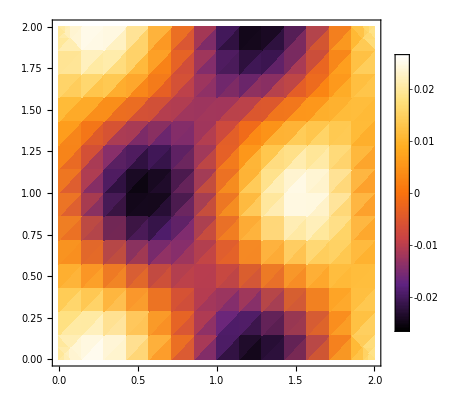

```mathematica
(* Truncated sph harmonic inner product *)
plS=DensityPlot[Chop[dotS[XA,Rot[Rangle[Pi*theta,Pi*phi,0],XB],lmax,sval]],{theta,0,2},{phi,0,2},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

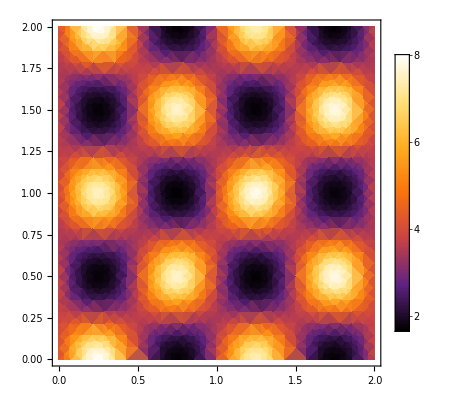

```mathematica
(* Full/direct gaussian inner product *)
plD=DensityPlot[dotD[XA,Rot[Rangle[Pi*theta,Pi*phi,0],XB],sval],{theta,0,2},{phi,0,2},ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

```mathematica
GraphicsRow[{plD,plS}]
```

-Graphics-